```mathematica
SetDirectory["/home/zah/github/OQSID-thesis/MODELS"];
Directory[]
(*A = Import["DMD_b4_LTI_trn4_2023-Nov-29_at_17-38.h5", "/gamma_0.079477/A"];*)
(*Subscript[Ac, SID] = Import["DMD_b4_LTI_trn4_2023-Nov-29_at_17-38.h5", "/gamma_0.079477/Ac"];*)
(* gamma = 0.0 0.079477 0.25133 0.79477 2.5133 7.9477 25.133 79.477 251.33*)
Subscript[Ac, SID] = Import["DMD_b4_LTI_trn4_2023-Nov-29_at_17-38.h5", "/gamma_0.25133/Ac"]

Subscript[b, x] :={1, 0, 0, 1}ᵀ;
Subscript[Ac, symb]= ({{-γ/2, ω, 0, 0}, {-ω, -γ/2, 0, 0}, {0, 0, -γ, γ}, {0, 0, 0, 0}});
ℐ[n_]:=IdentityMatrix[n];
TransferFunction[A_, b_]:= Assuming[{γ∈Reals,ω∈Reals},Simplify[Inverse[s*ℐ[4]- A].b]];
```

/home/zah/github/OQSID-thesis/MODELS

{{-5.45125×10^-8,25.1501,-0.00533117,-2.28992×10^-14},{-25.1327,-0.251386,-0.000621224,4.77622×10^-14},{0.0000563978,-0.000348851,-0.251773,7.86491×10^-14},{3.23583×10^-6,1.72616×10^-6,0.251014,-7.8412×10^-14}}

```mathematica
PolynomialDegree[0,varlist_]:=Undefined

PolynomialDegree[poly_,varslist_]:=Module[{epoly=Expand[poly]},If[!PolynomialQ[epoly,varslist],Message[Poly::notpoly,poly,varslist];Return[]];
If[Head[epoly]=!=Plus,Plus@@Exponent[epoly,varslist],Max@Map[(Plus@@Exponent[#,varslist])&,Level[epoly,1]]]]

Poly::notpoly="The input expression `1` is not a polynomial in the specified variable(s) `2`.";
```

```mathematica
Subscript[Gx, symb] =TransferFunction[Subscript[Ac, symb], Subscript[b, x] ]
Subscript[Gx, SID]=TransferFunction[Subscript[Ac, SID], Subscript[b, x] ]
```

{(2 (2 s+γ))/(4 s^2+4 s γ+γ^2+4 ω^2),-(4 ω)/(4 s^2+4 s γ+γ^2+4 ω^2),γ/(s^2+s γ),1/s}

{(2.99657×10^-13+0.063292 s+0.503159 s^2+s^3)/(0.+159.144 s+632.155 s^2+0.503159 s^3+s^4),(1.5544×10^-13-6.32775 s-25.1327 s^2)/(0.+159.144 s+632.155 s^2+0.503159 s^3+s^4),(4.9714×10^-11+0.00878177 s+0.0000563978 s^2)/(0.+159.144 s+632.155 s^2+0.503159 s^3+s^4),(159.146+632.155 s+0.503162 s^2+s^3)/(0.+159.144 s+632.155 s^2+0.503159 s^3+s^4)}

```mathematica
n= PolynomialDegree[Denominator[Subscript[Gx, SID][[2]]],s]-PolynomialDegree[Denominator[Subscript[Gx, symb][[2]]],s]
```

2

```mathematica
Canc[G_]:=(
d:=PolynomialDegree[Denominator[G],s];
c:= Coefficient[Denominator[G],s,d];
(Expand[s^n*Simplify[Numerator[G]/c]] )/(Expand[s^n*Simplify[Denominator[G]/c]])
);
```

```mathematica
eqv[p_]:=p==0;
eqvs :=Map[eqv, Flatten[CoefficientList[Numerator[Together[Subscript[Gx, SID] - Subscript[Gx, symb]]],s]]]
MatrixForm[eqvs ];
```

```mathematica
MatrixForm[Flatten[CoefficientList[Numerator[Together[Subscript[Gx, SID] - Subscript[Gx, symb]]],s]]]
```

(2.99657×10^-13 γ^2+1.19863×10^-12 ω^2
-318.287 γ+0.063292 γ^2+0.253168 ω^2
-636.575-1264.06 γ+0.503159 γ^2+2.01264 ω^2
-2528.37+1.00632 γ+1. γ^2+4. ω^2
-2.1805×10^-7+2. γ
1.5544×10^-13 γ^2+6.21762×10^-13 ω^2
6.21762×10^-13 γ-6.32775 γ^2+636.575 ω-25.311 ω^2
6.21762×10^-13-25.311 γ-25.1327 γ^2+2528.62 ω-100.531 ω^2
-25.311-100.531 γ+2.01264 ω
-100.531+4. ω
-159.144 γ
4.9714×10^-11-632.146 γ
0.00878177-0.503103 γ
0.0000563978-1. γ
0.00219363
-0.0000275984
3.23583×10^-6)

```mathematica
Solve[eqvs]
```

{}

```mathematica
Solve[{eqvs[[9]],eqvs[[10]]}]
```

{{γ→0.251386,ω→25.1327}}

```mathematica
expr:=Assuming[{_∈Reals},
Simplify[Total[Flatten[CoefficientList[Numerator[Together[Subscript[Gx, SID] - Subscript[Gx, symb]]],s]]^2]]]
```

```mathematica
Minimize[expr, {γ,ω}]
```

{6.50449×10^6,{γ→-0.377906,ω→-0.00208867}}

```mathematica
Show[Plot3D[expr, {γ,-1,1}, {ω,-10,30},
ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]],
AxesLabel ->{γ,ω}],PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
Show[Plot3D[Log[expr], {γ,0.4,0.5}, {ω,20,30},
ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]],
AxesLabel ->{γ,ω}],PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
DensityPlot[Log[expr], {γ,-1,1}, {ω,-30,30}]
```

-Graphics-

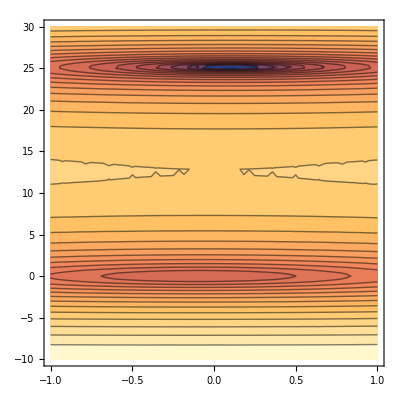

```mathematica
ContourPlot[Log[expr], {γ,-1,1}, {ω,-10,30}, Contours->20]
```

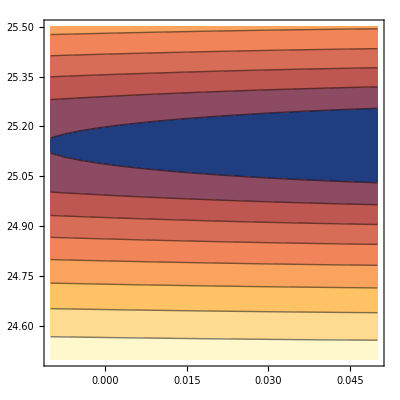

```mathematica
ContourPlot[Log[expr], {γ,-0.01,0.05}, {ω,24.5,25.5}]
```

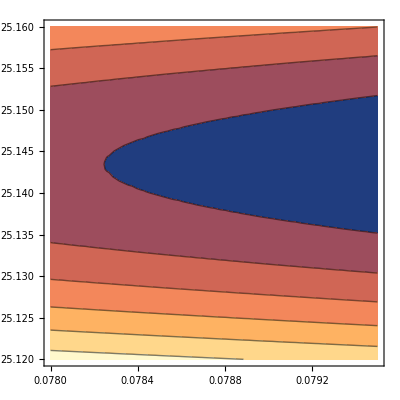

```mathematica
ContourPlot[Log[expr], {γ,0.078,0.0795}, {ω,25.12,25.16}]
```

```mathematica
w = Range[10,30,0.01];
g = Range[0,1,0.01];
(*Table[w,g]
f@@@{{a,b},{c,d}}*)
```

```mathematica
f[t_]:=ReplaceAll[expr, {γ-> t[[1]],ω -> t[[2]]}];
f[{0,10}]
```

2.51476×10^8

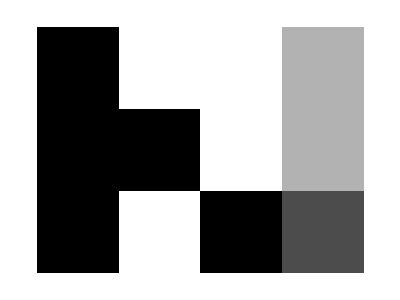

```mathematica
ArrayPlot[{{1,0,0,0.3},{1,1,0,0.3},{1,0,1,0.7}}]
```

```mathematica
(* M2:=Table[Log[expr],{γ,-1,1,0.01}, {ω,20,30, 0.01}]
ArrayPlot[M2]*)
```

```mathematica
Min[M2]
```

M2

```mathematica
Show[Plot3D[Log[expr], {γ,-1,1}, {ω,-10,30},
ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]],
AxesLabel ->{γ,ω}],PlotRange->All,PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
Minimize[expr,{γ,ω}]
```

{6.50449×10^6,{γ→-0.377906,ω→-0.00208867}}

```mathematica
(*ArrayPlot[Table[Log[expr],{γ,-30,30,0.01}, {ω,-30,30, 0.01}], AspectRatio->1]*)
```

```mathematica
(*ArrayPlot[Table[Log[expr],{γ,-1,1,0.01}, {ω,-30,30, 0.01}], AspectRatio->2]*)
```

```mathematica
DensityPlot[expr,{γ,-10,10}, {ω,-10,30}]
```

-Graphics-

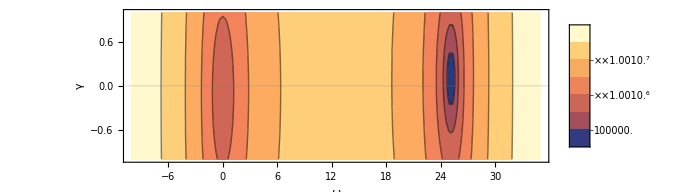

```mathematica
ContourPlot[expr, {ω,-10,35},{γ,-1,1}, 
ScalingFunctions->{ None, None,"Log10" },AxesLabel ->{γ,ω}, PlotLegends->Automatic,PlotRange->All, FrameLabel->{"ω","γ"}, AspectRatio->1/3, 
GridLines->{None,{0}}, ImageSize->Large]
```

```mathematica
DensityPlot[expr,  {ω,24,26}, {γ,0,0.5}, ScalingFunctions->{ "Log10", "Log10","Log10" }]
```

-Graphics-

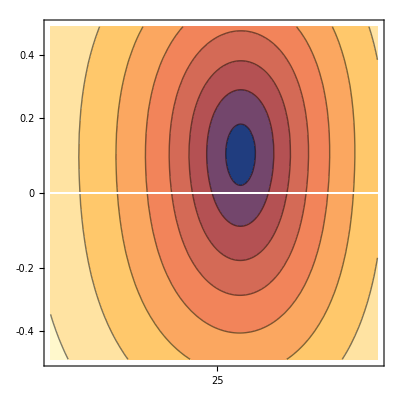

```mathematica
ContourPlot[expr,  {ω,24,26}, {γ,-0.5,0.5}, ScalingFunctions->{ "Log10", "SignedLog","Log10" }]
```

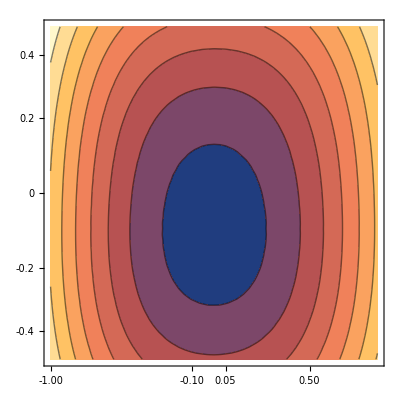

```mathematica
ContourPlot[expr,  {ω,-1,1}, {γ,-0.5,0.5}, ScalingFunctions->{"SignedLog", "SignedLog","Log10" }]
```

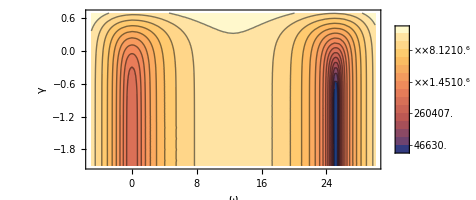

```mathematica
ContourPlot[expr, {ω,-5,30},{γ,-3,5}, ScalingFunctions->{ None, "Log10","Log" }, PlotLegends->Automatic, FrameLabel->{"ω","γ"}, Contours->15, AspectRatio->1/2]
```

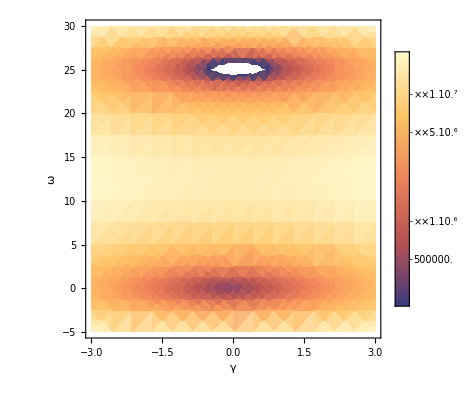

```mathematica
DensityPlot[expr, {γ,-3,3}, {ω,-5,30},ScalingFunctions->"Log", PlotLegends->Automatic, AxesLabel ->{"γ","ω"}, AspectRatio->1]
```

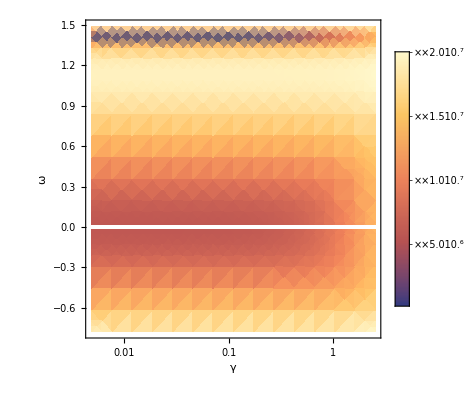

```mathematica
DensityPlot[expr, {γ,-2.5,2.5}, {ω,-5,30},ScalingFunctions->{"Log","SignedLog","SignedLog"}, AxesLabel ->{"γ","ω"},PlotLegends->Automatic]
```